```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\El Babbel\Desktop\Studium\GP2

```mathematica
ReadList["linear.txt"]
```

{0.,15.6,32.64,51.84,125.44,196.,280.8,285.6,411.84,577.8}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
linear = ReadList["linear.txt",{Real,Real,Real}]
```

{{0.,2.8,1.},{2.,5.2,1.5},{4.,6.8,1.2},{6.,9.6,0.9},{8.,11.2,1.4},{10.,14.,1.4},{12.,15.6,1.5},{14.,17.,1.2},{16.,19.8,1.3},{18.,21.4,1.5}}

```mathematica
MatrixForm[linear]
```

(0. | 2.8 | 1.
2. | 5.2 | 1.5
4. | 6.8 | 1.2
6. | 9.6 | 0.9
8. | 11.2 | 1.4
10. | 14. | 1.4
12. | 15.6 | 1.5
14. | 17. | 1.2
16. | 19.8 | 1.3
18. | 21.4 | 1.5)

```mathematica
x = linear[[All,1]]
```

{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.}

```mathematica
y = linear[[All,2]]
```

{2.8,5.2,6.8,9.6,11.2,14.,15.6,17.,19.8,21.4}

```mathematica
δy = linear[[All,3]]
```

{1.,1.5,1.2,0.9,1.4,1.4,1.5,1.2,1.3,1.5}

```mathematica
n = Length[x]
```

10

```mathematica
s = ∑_(i=1)^n 1 / (δy[[i]])^2 *∑_(i=1)^n (x[[i]])^2 / (δy[[i]])^2 - (∑_(i=1)^n x[[i]] / (δy[[i]])^2 )^2 //N
```

1395.94

```mathematica
a0 = 1/s *(∑_(i=1)^n (x[[i]])^2 / (δy[[i]])^2  * ∑_(i=1)^n y[[i]]/ (δy[[i]])^2  - ∑_(i=1)^n x[[i]] / (δy[[i]])^2  *∑_(i=1)^n (x[[i]] * y[[i]]) / (δy[[i]])^2) //N
```

3.01566

```mathematica
b0 = 1/s *(∑_(i=1)^n 1/ (δy[[i]])^2  * ∑_(i=1)^n (x[[i]] * y[[i]])/ (δy[[i]])^2  - ∑_(i=1)^n x[[i]] / (δy[[i]])^2  *∑_(i=1)^n y[[i]] / (δy[[i]])^2)
```

1.03634

```mathematica
Δa0 = Sqrt[1 / s *(∑_(i=1)^n x[[i]]^2/(δy[[i]])^2)]
```

0.675303

```mathematica
Δb0 = Sqrt[1 / s * (∑_(i=1)^n 1 / (δy[[i]])^2)] //N
```

0.0685982

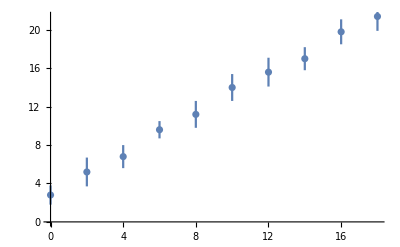

```mathematica
ErrorListPlot[linear]
```

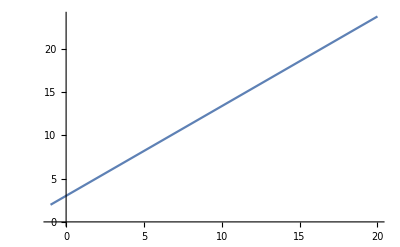

```mathematica
Plot[a0 + b0 t,{t,-1,20}]
```

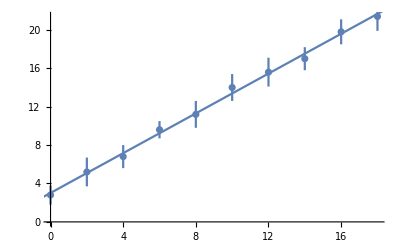

```mathematica
Show[ErrorListPlot[linear],Plot[a0+b0 t,{t,-1,20}]]
```

```mathematica
LinReg[daten_]:=Module[{x,y,δy,s,Δa0,Δb0,a0,b0,n},
n = Length[daten];
x = daten[[All,1]];
y = daten[[All,2]];
δy = daten[[All,3]];
s = ∑_(i=1)^n 1 / (δy[[i]])^2 *∑_(i=1)^n (x[[i]])^2 / (δy[[i]])^2 - (∑_(i=1)^n x[[i]] / (δy[[i]])^2 )^2;
a0 = 1/s *(∑_(i=1)^n (x[[i]])^2 / (δy[[i]])^2  * ∑_(i=1)^n y[[i]]/ (δy[[i]])^2  - ∑_(i=1)^n x[[i]] / (δy[[i]])^2  *∑_(i=1)^n (x[[i]] * y[[i]]) / (δy[[i]])^2);
b0 = 1/s *(∑_(i=1)^n 1/ (δy[[i]])^2  * ∑_(i=1)^n (x[[i]] * y[[i]])/ (δy[[i]])^2  - ∑_(i=1)^n x[[i]] / (δy[[i]])^2  *∑_(i=1)^n y[[i]] / (δy[[i]])^2);
Δa0 = Sqrt[1 / s *(∑_(i=1)^n x[[i]]^2/(δy[[i]])^2)];
Δb0 = Sqrt[1 / s * (∑_(i=1)^n 1 / (δy[[i]])^2)];
Print["Berechnung der Fehler aus den Eingangsfehlern"];
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0}} ]];
{b -> b0,Δb -> Δb0,a -> a0,Δa-> Δa0}
]
```

```mathematica
regerg = LinReg[linear]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 1.03634 | 0.0685982
Achsenabschnitt a | 3.01566 | 0.675303

{b→1.03634,Δb→0.0685982,a→3.01566,Δa→0.675303}

```mathematica
a /. regerg
```

3.01566

```mathematica
b/.regerg
```

1.03634

```mathematica
Δa/. regerg
```

0.675303

```mathematica
Δb /. regerg
```

0.0685982

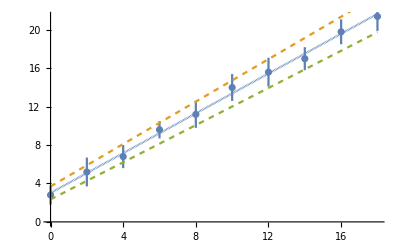

```mathematica
Show[ErrorListPlot[linear],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.regerg],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

```mathematica
(exponential = ReadList["exp.txt",{Real,Real,Real}])//TableForm[#,TableHeadings->{{},{"X","Y","ΔY"}}]&
```

| X | Y | ΔY
 | 0. | 82. | 1.
 | 2. | 56. | 1.
 | 4. | 37. | 1.
 | 6. | 26. | 1.
 | 8. | 18. | 1.
 | 10. | 11. | 1.
 | 12. | 9. | 1.
 | 14. | 5. | 1.
 | 16. | 3. | 1.

```mathematica
(linearisiert = Replace[exponential,{xi_,yi_,Δyi_}->{xi,Log[yi], Δyi/ yi},2]) //TableForm[#,TableHeadings->{{},{"X","Ln(Y)","ΔLn(Y)=Δyi/ yi"}}]&
```

| X | Ln(Y) | ΔLn(Y)=Δyi/ yi
 | 0. | 4.40672 | 0.0121951
 | 2. | 4.02535 | 0.0178571
 | 4. | 3.61092 | 0.027027
 | 6. | 3.2581 | 0.0384615
 | 8. | 2.89037 | 0.0555556
 | 10. | 2.3979 | 0.0909091
 | 12. | 2.19722 | 0.111111
 | 14. | 1.60944 | 0.2
 | 16. | 1.09861 | 0.333333

```mathematica
experg = LinReg[linearisiert]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | -0.193466 | 0.00365475
Achsenabschnitt a | 4.40686 | 0.010881

{b→-0.193466,Δb→0.00365475,a→4.40686,Δa→0.010881}

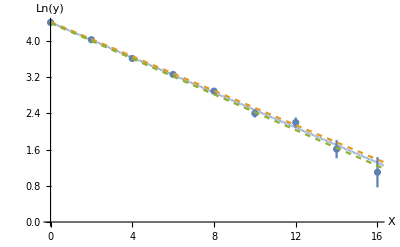

```mathematica
Show[ErrorListPlot[linearisiert,AxesLabel->{"X","Ln(y)"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.experg],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```